# Series expanding the bands of La_3 Ni_2 O_7

Anirudh Chandrasekaran

Loughborough University
18 June 2024

## Loading the library

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/La3Ni2O7"]<>"Package"];
<<BandUtilitiesExtras`
```

## Loading and analysing the tight binding model

We first load the tight binding model (with symmetrisation) on to a matrix and use it to define the Hamiltonian

To compare with the unsymmetrised model, we load it as well

```mathematica
EF=0.9853;
Hamltn1[k1_,k2_]=LoadTBM[NotebookDirectory[]<>"La3Ni2O7_Amam_Monolayer_3eV.dat","FileType"->"Wannier90","Messages"->False][[1]]-DiagonalMatrix[ConstantArray[EF,8]];
```

### The effect of the symmetrisation on the weak splitting

Eigenvalues of the model at the (π, 0)

```mathematica
Sort[Eigenvalues[Hamltn1[π,0]//N]]
```

{-0.24462,-0.243889,0.811291,0.811702,0.892884,0.893831,0.901769,0.902166}

### The band structures

For the sake of plotting the band structure and series expanding, we redefine the Hamiltonian

```mathematica
Hamltn1New[k_]:=Hamltn1[k[[1]],k[[2]]]
```

We can now plot the band structure. Firstly let us define the path

```mathematica
HSymmPts={{{0,π},"Y"},{{0,0},"Γ"},{{π,0},"X"},{{π,π},"M"},{{0,0},"Γ"},{{-π,π},"M_p"}};
```

and generate the band structure data

```mathematica
Bands1=GenerateBandStructure[Hamltn1New,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,3,5,7},{2,4,6,8}},"TotalPoints"->400];
```

We have grouped all the d_(z^2) orbitals together, and likewise the d_(x^2-y^2) orbitals as well, for the sake of orbital projections.

We call the PlotBandStructure routine

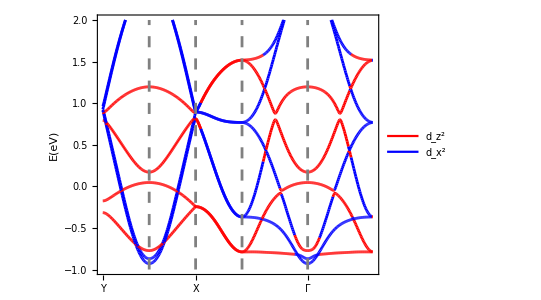

```mathematica
plt1=PlotBandStructure[Bands1,{-1,2},"PlotKeyLegend"->{{"d_(z^2)","d_(x^2)"},{0.09,0.85}},"LineColorScheme"->{Red,Blue},"yLabel"->{"E(eV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"}]
```

## Locating the (possible) critical point located between the M and Γ points

For the LocateCriticalPoint routine, we first identify an approximate range for “critical” points in bands 3 and 4.

```mathematica
kp1=HSymmPts[[4,1]]+0.5(HSymmPts[[5,1]]-HSymmPts[[4,1]]);
kp2=HSymmPts[[4,1]]+0.75(HSymmPts[[5,1]]-HSymmPts[[4,1]]);
```

```mathematica
kcrit3=LocateCriticalPoint[Hamltn1New,kp1,kp2,3,"MaxIterations"->20][[1]]
```

The value of MaxIterations has been reset to 20.

Point found after 14 iteration(s).

{1.31036,1.31036}

```mathematica
kcrit4=LocateCriticalPoint[Hamltn1New,kp1,kp2,4,"MaxIterations"->30,"Resolution"->10^-6][[1]]
```

The value of MaxIterations has been reset to 30.

Point found after 20 iteration(s).

{1.24668,1.24668}

Below we will see that these are not genuine critical points. The directional derivative along the MΓ direction vanishes but not the gradient itself.

## Series expanding the band structure

We will attempt to series expand the band structure at some points of interest near the Fermi level.

### The Y point

We notice a VHS at the Y point on band 2. We confirm this first with the symmetrised model and then the unsymmetrised model

```mathematica
TaylorExpandBand[Hamltn1New,{0,π}//N,2,4(*,"Resolution"->10^-8,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{-0.175003,0,-0.116074 k_x^2+0.00150665 k_x k_y+0.206088 k_y^2,0,-0.00183652 k_x^4-0.00180483 k_x^3 k_y+0.172471 k_x^2 k_y^2-0.0130803 k_x k_y^3-0.388893 k_y^4}}

So this is an ordinary saddle with log diverging DOS

### The Γ point

The Γ point seems to host a maximum on band 4, near the Fermi level

```mathematica
TaylorExpandBand[Hamltn1New,{0,0}//N,4,4(*,"Resolution"->10^-8,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{0.0456275,0,-0.0291695 k_x^2+0.00225983 k_x k_y-0.0287074 k_y^2,0,-0.000610605 k_x^4-0.00464882 k_x^3 k_y-0.00605766 k_x^2 k_y^2-0.00310384 k_x k_y^3+0.000612562 k_y^4}}

Indeed, this is a maximum that once again has log diverging DOS below the maximum energy and zero DOS above.

### The X point

The X point is the one of the most interesting of the lot since it appears to have a pair of Van Hove singularities in both the models. Let us confirm that explicitly

```mathematica
TaylorExpandBand[Hamltn1New,{π,0}//N,4,2,"Resolution"->10^-3(*,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{0.811291,-0.217837 k_x,-2.78856 k_x^2+0.00737567 k_x k_y-2.13615 k_y^2},{0.811702,0.217837 k_x,-2.80123 k_x^2+0.00653128 k_x k_y-2.14467 k_y^2}}

The series expansion indicates an interesting anomaly: neither of the bands have a VHS or for that matter a critical point thanks to the linear in k_x term. This might seem to contradict the π rotation symmetry at the X point that would normally force an isolated band to have critical point. But this is not necessary when we have multiple bands intersecting. In fact we see that the pair of bands together respect the π rotation symmetry at the X point!

Furthermore, from the band structure the starkly linear behaviour of the dispersion at the X point in the X-Γ direction is quite apparent (see below)

### The M point

The bands of interest are 3 and 4 which are located below the Fermi level

```mathematica
TaylorExpandBand[Hamltn1New,{π,π}//N,3,2,"Resolution"->10^-3(*,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{-0.367799,-0.0124961 k_x,0.201839 k_x^2+0.191851 k_y^2},{-0.367794,0.0124961 k_x,0.201839 k_x^2+0.191851 k_y^2}}

Similar to the case of the X point, we once again have a small linear dispersion for each band which nevertheless satisfy the π rotation symmetry jointly.

### The “critical” point located on the MΓ line

Having previously found the location of these points for bands 3 and 4, we compute the

```mathematica
Tayl1=TaylorExpandBand[Hamltn1New,kcrit3,3,2,"Resolution"->10^-4(*,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{-0.0838476,0.00609075 k_x-0.00601557 k_y,-0.820285 k_x^2-1.66029 k_x k_y-0.797172 k_y^2}}

```mathematica
Tayl2=TaylorExpandBand[Hamltn1New,kcrit4,4,2,"Resolution"->10^-4(*,"Dimension"->2*),"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{-0.0493854,-0.0140342 k_x+0.0140353 k_y,0.592806 k_x^2+1.36729 k_x k_y+0.788481 k_y^2}}

We notice once again that the bands in question do not have a critical point owing to the presence of a non-zero linear part for the dispersion. It is not surprising however that the band structure seemed to indicate a pair of critical points since the directional derivatives along the MΓ direction (i.e the (1,1) direction) vanish as can be seen explicitly:

```mathematica
Chop[Tayl1[[1,2]]/.{Subscript[k, x]->1,Subscript[k, y]->1},10^-4]
```

0

```mathematica
Chop[Tayl2[[1,2]]/.{Subscript[k, x]->1,Subscript[k, y]->1},10^-4]
```

0

## DOS behaviour near the high symmetry points, close to the Fermi level

We can now mark the DOS behaviour based on the inference drawn from the series expansions derived above. We first note the locations of the critical points on the band structure plot we previously generated:

```mathematica
Bands1[[2]]
```

{{0,Y},{π,Γ},{2 π,X},{3 π,M},{3 π+√2 π,Γ},{3 π+2 √2 π,M_p}}

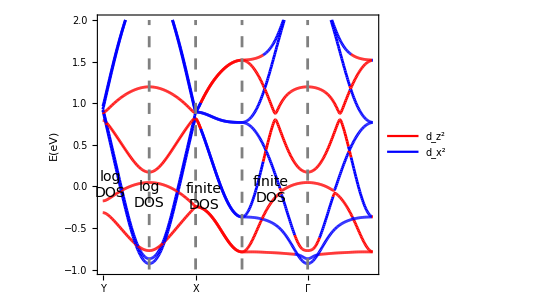

```mathematica
Show[{plt1,Graphics[Text[Style["log\nDOS",FontFamily->"Times",FontSize->14],{π,-0.1}]],Graphics[Text[Style["log\nDOS",FontFamily->"Times",FontSize->14],{π/6.5,0.02}]],Graphics[Text[Style["finite\nDOS",FontFamily->"Times",FontSize->14],{2.175π,-0.13}]],Graphics[Text[Style["finite\nDOS",FontFamily->"Times",FontSize->14],{(3+√2/2.3)π,-0.04}]]},ImageSize->Full]
```